```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["data.xlsx"];
```

```mathematica
CdSe=data[[1]][[14;;56,2;;3]]
```

{{6665.9,1.96},{6625.73,1.56},{6542.04,0.97},{6458.35,0.82},{6374.66,0.74},{6290.97,0.67},{6207.28,0.6},{6123.59,0.54},{6039.9,0.49},{5956.21,0.45},{5872.52,0.41},{5788.83,0.35},{5705.14,0.31},{5621.45,0.28},{5537.76,0.25},{5454.07,0.22},{5370.38,0.21},{5286.69,0.19},{5203.,0.17},{5119.31,0.16},{5035.62,0.14},{4951.93,0.13},{4868.24,0.12},{4784.55,0.11},{4700.86,0.1},{4617.17,0.09},{4533.48,0.08},{4449.79,0.067},{4366.1,0.062},{4282.41,0.055},{4198.72,0.05},{4115.03,0.046},{4031.34,0.042},{3947.65,0.037},{3863.96,0.034},{3780.27,0.03},{3696.58,0.028},{3612.89,0.027},{3529.2,0.025},{3445.51,0.023},{3361.82,0.021},{3278.13,0.02},{3194.44,0.017}}

General::munfl: 1./(4.26887137326424×10^5789) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -3.57989×10^-18 3.04788087666257×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{a→0.,b→1.}

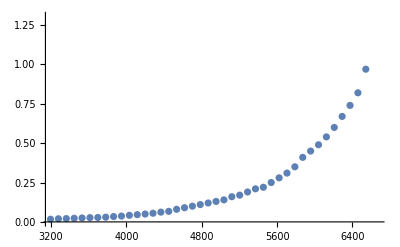

```mathematica
CdSeFit=FindFit[CdSe,{a Exp[b*x]},{a,b},x]
Show[ListPlot[CdSe],Plot[CdSeFit,{x,Min[CdSe[[All,1]]],Max[CdSe[[All,1]]]}]]
```